## general definitions

```mathematica
CL=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
cm=10^(-2);
mm=10^(-3);
milli=10^-3;
μm=10^(-6);
nm=10^(-9);

kilo=10^3;
mega=10^6;
giga=10^9;
terra=10^12;

au=1.66 10^-27;

cl=299792458;

eVal=1.602 10^-19;
ϵ0Val=8.854 10^-12;

hPlanck=6.626 10^-34;

mCa=39.96 au;
mCaH=41 au;
mCaO=56au;
mCaOH=57au;
```

```mathematica
FWHMtoWaist[FWHM_]:=FWHM/(2Sqrt[1/2Log[2]])
```

## general functions

```mathematica
Clear[ZeroToOne];
ZeroToOne[data_]:=Module[{minVal,maxVal},
minVal=Min[data];
maxVal=Max[data];
(data-minVal)/(maxVal-minVal)
];
```

```mathematica
Clear[CustomZeroToOneA];
CustomZeroToOneA[data_]:=Module[{frequData,countsData},
frequData=data[[All,1]];
countsData=ZeroToOne[data[[All,2]]];
Table[{frequData[[k]],countsData[[k]]},{k,1,Length[frequData]}]
];
```

## two ions - trap frequency

### final trap frequency functions

```mathematica
TrapFreq2Ions[tfCa_,m1_,m2_,mca_:mCa]:=√(((m1+m2-√(m1^2-m1 m2+m2^2)) mca)/(m1 m2)) tfCa
```

```mathematica
FindMass[tf_,tfCa_,mca_:mCa,amu_:au]:=(mca tfCa^2 (2 tf^2-3 tfCa^2))/(tf^2 (tf^2-2 tfCa^2))1/amu
ΔFindMass[tf_,Δtf_,tfCa_,ΔtfCa_,mca_:mCa,amu_:au]:={FindMass[tf,tfCa,mca,amu],4 √((mca^2 tfCa^2 (tf^4-3 tf^2 tfCa^2+3 tfCa^4)^2 (tfCa^2 Δtf^2+tf^2 ΔtfCa^2))/(tf^6 (tf^2-2 tfCa^2)^4))1/amu}
```

### specific values

```mathematica
TrapFreq2Ions[526.8 kilo,mCa,mCaOH,mCa]/kilo
```

474.704

```mathematica
ΔFindMass[474.9kilo,0.2kilo,526.8 kilo,0.2kilo]
```

{56.9295,0.0967024}

```mathematica
tfmCaO=TrapFreq2Ions[526.752kilo,mCa,mCaO,mCa]/kilo
tfmCaOH=TrapFreq2Ions[526.752kilo,mCa,mCaOH,mCa]/kilo
tfmCaOH2=TrapFreq2Ions[526.752kilo,mCa,mCaOH +1 au,mCa]/kilo
{tfmCaO-tfmCaOH,tfmCaOH-tfmCaOH2}
```

477.459

474.66

471.896

{2.79893,2.76481}

## workspace

### functions

```mathematica
Clear[GaussFitI];
GaussFitI[Data_,ShowPlot_:False]:=Module[{minFrequ,fit,output},
minFrequ=Data[[Position[Data[[All,2]],Min[Data[[All,2]]]][[1,1]],1]];
fit=NonlinearModelFit[Data,1-o-a Exp[-2(f-f0)^2/FWHMtoWaist[FWHM]^2],{{f0,minFrequ},{o,0.8},{a,0.8},{FWHM,1}},f];
If[ShowPlot,
Print[
Show[
ListPlot[{Data,Data},PlotRange->All,Joined->{True,False},PlotStyle->{CL[[1]],CL[[1]]}],
Plot[fit[x],{x,Min[Data[[All,1]]],Max[Data[[All,1]]]},PlotStyle->Red,PlotRange->All]]]
];
output=fit
];
```

```mathematica
Clear[AnalysisFuncI];
AnalysisFuncI[Path_,ShowPlot_:False]:=Module[{PathsRef,PathsSpec,RefFiles,EventFiles,StringList,MSpecFiles,RefData1,RefData2,MSpecData1,MSpecData2,RefFit,RefFrequ,MSpecFit,MassTable,output},
PathsRef=Select[FileNames["*",Path,1],StringContainsQ[#,"frequ_ref"]&][[1]];
PathsSpec=Select[FileNames["*",Path,1],StringContainsQ[#,"mass_spectrometry"]&];
RefFiles=Select[FileNames["*",PathsRef,2],StringContainsQ[#,"trap_freq_scan.txt"]&];
EventFiles=FileNames["*",PathsSpec,1];
StringList={"trap_freq_scan_1.txt","trap_freq_scan_2.txt","trap_freq_scan_3.txt","trap_freq_scan_4.txt","trap_freq_scan_5.txt"};
MSpecFiles=Table[Select[FileNames["*",EventFiles[[k]],2],StringContainsQ[#,StringList]&],{k,1,Length[EventFiles]}];
RefData1=Table[Delete[Import[RefFiles[[k]],"Table"],1][[All,{1,2}]],{k,1,Length[RefFiles]}];
RefData2=CustomZeroToOneA[Table[{RefData1[[1,k,1]],Total[RefData1[[All,k,2]]]},{k,1,Length[RefData1[[1]]]}]];
MSpecData1=Table[Table[Delete[Import[MSpecFiles[[k,n]],"Table"],1][[All,{1,2}]],{n,1,Length[MSpecFiles[[k]]]}],{k,1,Length[MSpecFiles]}];
MSpecData2=Table[CustomZeroToOneA[Table[{MSpecData1[[k,1,n,1]],Total[MSpecData1[[k,All,n,2]]]},{n,1,Length[MSpecData1[[k,1]]]}]],{k,1,Length[MSpecData1]}];
RefFit=GaussFitI[RefData2,ShowPlot];
RefFrequ=RefFit[[1,2,1,2]];
MSpecFit=Table[GaussFitI[MSpecData2[[k]],ShowPlot],{k,1,Length[MSpecData2]}];
MassTable=Table[Join[ΔFindMass[MSpecFit[[k,1,2,1,2]]kilo,200,RefFrequ kilo,200,mCa,au],{MSpecFit[[k,1,2,1,2]],RefFrequ}],{k,1,Length[MSpecFit]}];
output={MassTable,MSpecFit,MSpecData2,RefFit,RefData2}
];
```

### anlysis

```mathematica
Paths=Select[FileNames["*",NotebookDirectory[]<>"\\mass_spec_data",1],StringContainsQ[#,"run_"]&];
```

```mathematica
AllData=Table[AnalysisFuncI[Paths[[k]]],{k,1,Length[Paths]}];
HistData=Flatten[AllData[[All,1]],1][[All,1]]
```

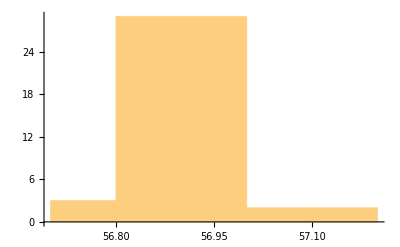

```mathematica
Histogram[HistData,5]
```

### all plots

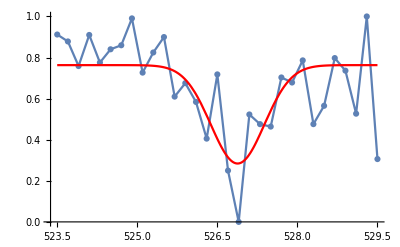

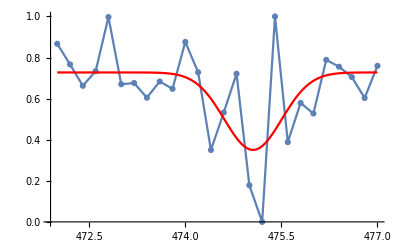

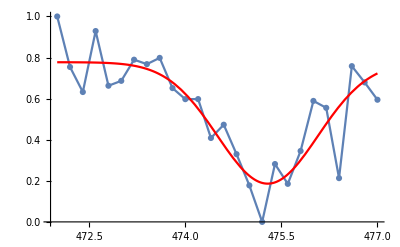

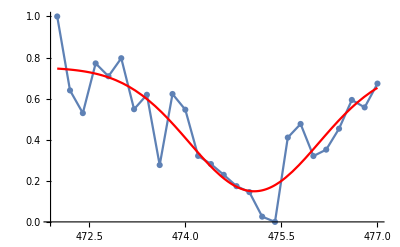

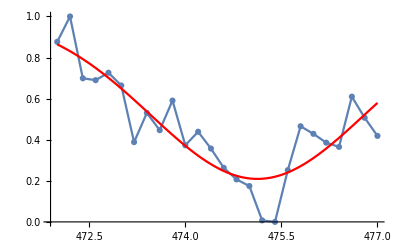

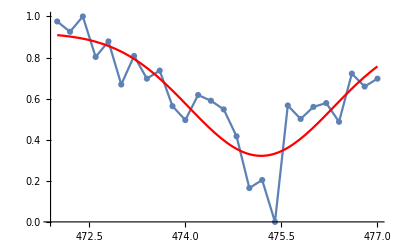

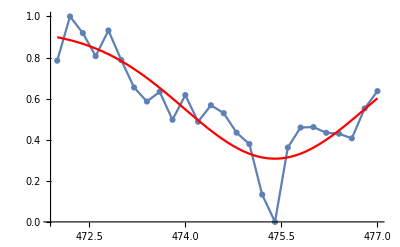

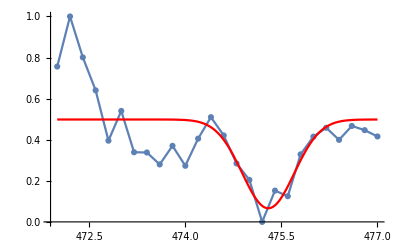

```mathematica
Flatten[Table[AnalysisFuncI[Paths[[k]],True],{k,1,Length[Paths]}],1];
```